```mathematica
data={{0,1}}; (*setting up a dataset to which the Do loop data will be sent to. includes initial condition y(0)=1*)
h=0.1; (*step size*)
y0=1;(*initial condition that will be used in the Do loop*)
```

```mathematica
Do[y1=y0+((x-0.1)+y0)*h; AppendTo[data,{x,y1}]; y0=y1, {x,0.1,10,h}] (*calculating y(x+h)=y(x)+y'(x)*h with y'(x)=x+y and h=0.1 from x=0.1 to x=10 (x=0 is already included in the data set). for each iteration, the (x+h, y(x+h)) data is stored in the set "data" defined earlier.*)
```

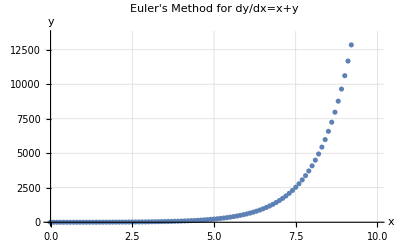

```mathematica
ListPlot[data,PlotLabel->"Euler's Method for dy/dx=x+y",GridLines->Automatic,AxesLabel->{"x","y"}](*plotting the data in the set "data", labeling the plot, setting up gridlines, and labeling the axes.*)
```